# Generating Training set and Test set

```mathematica
ClearAll["Global`*"]
```

```mathematica
getRandomPointsList[range_Integer,n_Integer,i_Integer]:=Table[RandomReal[range,{n,2}],i]
```

```mathematica
getRandomPointsList[10,10,10]
```

{{{2.22773,6.63688},{4.63365,7.91644},{0.624429,8.07387},{0.521976,2.67508},{1.10755,3.87239},{2.92475,4.6557},{2.28652,4.85331},{6.7229,5.10579},{5.54092,6.80956},{4.11041,2.40147}},{{4.78549,7.6826},{7.12604,7.18501},{8.22495,2.44984},{5.95536,6.84752},{4.85678,1.6037},{8.13975,4.89809},{5.35499,5.43415},{3.29235,2.66646},{4.81009,1.90751},{3.06677,4.46127}},{{0.372972,7.08093},{2.60013,6.4792},{0.856684,6.89193},{4.14518,1.50655},{0.249583,6.08129},{6.61138,5.57163},{1.77447,6.44077},{7.8377,2.7721},{9.90968,9.11507},{5.86363,2.33053}},{{2.86977,0.640061},{5.85659,0.396341},{3.90074,2.4059},{4.74789,6.44948},{0.17093,9.49526},{3.91275,5.72524},{3.19232,9.32445},{9.34072,8.721},{2.85901,7.40291},{1.53862,5.52196}},{{4.12743,7.7754},{1.82155,4.14466},{4.32358,5.36804},{9.44049,5.36863},{9.57423,3.89922},{4.69568,3.10304},{1.17199,1.32451},{3.65164,1.18061},{5.14641,1.55101},{2.1419,5.25386}},{{6.6118,8.17572},{6.57447,3.58226},{4.88023,4.30433},{1.51974,2.79686},{5.68476,0.156216},{7.061,6.48818},{8.51718,8.56359},{4.05935,2.43918},{8.68098,2.62384},{1.47435,3.72874}},{{7.7862,4.33129},{5.35903,6.94013},{7.28391,3.69871},{9.20544,6.35126},{9.04599,9.89779},{6.03655,4.43191},{0.825138,7.39091},{1.0083,2.95158},{8.39108,5.6144},{2.69678,5.32145}},{{6.16086,7.13512},{1.66509,4.66878},{2.94741,9.52097},{2.86392,6.89821},{5.69246,6.96302},{4.51514,1.68607},{5.18733,8.68748},{2.90062,8.68484},{2.75308,2.17405},{2.83715,5.41776}},{{7.93917,7.49149},{2.57923,1.15915},{5.34619,4.15172},{3.04493,0.492323},{7.0568,7.53686},{1.60775,1.30316},{2.47539,0.550468},{2.26585,3.20256},{4.67646,5.68355},{9.21745,3.3482}},{{6.4894,3.09142},{5.72057,0.288601},{3.29468,2.12666},{8.54358,8.31525},{4.52437,6.75754},{8.52046,8.56664},{1.76469,7.21103},{1.64435,7.00505},{1.22645,6.17091},{2.84618,7.13229}}}

```mathematica
getRasterizedPlots[data_]:=Map[Rasterize[ListPlot[#],ImageSize->{1024,512}]&,data]
```

```mathematica
getRasterizedPlots[getRandomPointsList[10,10,10]]
```

```mathematica
ImageDimensions/@getRasterizedPlots[getRandomPointsList[10,10,10]]
```

{{1024,512},{1024,512},{1024,512},{1024,512},{1024,512},{1024,512},{1024,512},{1024,512},{1024,512},{1024,512}}

```mathematica
getRawAxes[data_]:=Map[AlphaChannel[Rasterize[ListPlot[#,PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None,ImageSize->{1024,512}]]&,data]
```

```mathematica
getRawAxes[getRandomPointsList[10,10,10]]
```

```mathematica
getRawLabels[data_,axes_]:=MapThread[ImageDifference[Binarize[AlphaChannel[Rasterize[ListPlot[#1,PlotStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None,ImageSize->{1024,512}]],0],#2]&,
{data,axes}
]
```

```mathematica
Module[{data=getRandomPointsList[10,10,10],axes},
axes=getRawAxes[data];
getRawLabels[data,axes]
]
```

```mathematica
getBinarizedPoints[data_]:=Map[AlphaChannel[Rasterize[ListPlot[#,AxesStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None,ImageSize->{1024,512}]]&,data]
```

```mathematica
getBinarizedPoints[getRandomPointsList[10,10,10]]
```

```mathematica
getAxes[axes_,binarizedPoints_]:=MapThread[ImageSubtract[#1,#2]&,{axes,binarizedPoints}]
```

```mathematica
getLabels[binarizedPoints_,labels_]:=MapThread[ImageSubtract[#1,#2]&,{labels,binarizedPoints}]
```

```mathematica
getBackgrounds[axes_,labels_,binarizedPoints_]:=MapThread[ColorNegate[ImageAdd[#1,#2,#3]]&,{axes,labels,binarizedPoints}]
```

```mathematica
Module[{data=getRandomPointsList[10,10,10],binarizedPoints,axes,labels},
binarizedPoints=getBinarizedPoints[data];
axes=getAxes[getRawAxes[data],binarizedPoints];
labels=getLabels[binarizedPoints,getRawLabels[data,axes]];
getBackgrounds[axes,labels,binarizedPoints]
]
```

```mathematica
segmentateImage[background_,axes_,labels_,binarizedPoints_]:=Round[ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background,axes,labels,binarizedPoints},"Real32"],{0,1,2,3}}]]];
```

```mathematica
getSegmentations[dataPoints_]:=Module[{data=dataPoints,binarizedPoints,axes,labels,backgrounds},
binarizedPoints=getBinarizedPoints[data];
axes=getAxes[getRawAxes[data],binarizedPoints];
labels=getLabels[binarizedPoints,getRawLabels[data,axes]];
backgrounds=getBackgrounds[axes,labels,binarizedPoints];
MapThread[segmentateImage[#1,#2,#3,#4]&,{backgrounds,axes,labels,binarizedPoints}]
]
```

```mathematica
createTrainingData[range_Integer,n_Integer,i_Integer]:=Module[{data=getRandomPointsList[range,n,i],plotsImages,segmentations},
plotsImages= getRasterizedPlots[data];
segmentations = getSegmentations[data];
MapThread[Rule[#1,#2]&,{plotsImages,segmentations}]
]
```

### Code to generate the training set and test set

```mathematica
ClearAll["Global`*"];

(* genetaring random 2D points for the plots *)
getRandomPointsList[range_Integer,n_Integer,i_Integer] := Table[ RandomReal[range, {n,2}], i ]

(**)
getRasterizedPlots[data_] := Map[Rasterize[ListPlot[#], ImageSize->{1024,512}] &, data]
```

### Sample of training set

```mathematica
trainingSet= createTrainingData[50,50,10];
```

```mathematica
x=trainingset;
```

```mathematica
MinMax[x[[1,2]]]
```

{1,7}

```mathematica
trainingSet[[All,2]]+=1;
```

```mathematica
{{1,2},{a,b}}[[All,1]]
```

{1,a}

```mathematica
Keys@{1->a,2->b}
```

{1,2}

```mathematica
Values@{1->a,2->b}
```

{a,b}

```mathematica
trainingSet[[1]]
```

```mathematica
trainingSet//Values
```

```mathematica
Map[MinMax,KtrainingSet]
```

{{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.}}

### NetTrain with Training data

```mathematica
data=createTrainingData[50,50,10];
```

```mathematica
trainingset=Take[data,8];
testset=Take[data,-2];
```

```mathematica
net=NetModel["Dilated ResNet-22 Trained on Cityscapes Data"]
```

NetGraph[<>]

```mathematica
net=NetModel["Dilated ResNet-22 Trained on Cityscapes Data","UninitializedEvaluationNet"]
```

NetGraph[<>]

```mathematica
initNet=NetInitialize@net
```

NetGraph[<>]

```mathematica
NetExtract[net,"Output"]
```

```mathematica
NetInitialize@NetChain[,"Output"->NetDecoder[{"Class",{0,1,2,3}}]]
```

NetChain::argx: NetChain called with 3 arguments; 1 argument is expected.

NetInitialize::arg1: First argument to NetInitialize should be a net or list of nets.

NetInitialize[$Failed]

```mathematica
encData=Normal@NetExtract[net,"input_0"];
{mean,var}=Lookup[encData,{"MeanImage","VarianceImage"}];
```

```mathematica
classdecoder=NetDecoder[{"Class",{0,1,2,3}}]
```

```mathematica
classdecoder=NetDecoder[{"Class",{"background","axes","labels","binarizedPoints"}}]
```

```mathematica
net=NetModel["Dilated ResNet-22 Trained on Cityscapes Data"]
```

NetGraph[<>]

```mathematica
NetGraph[]
```

```mathematica
our=NetReplacePart[net,{"input_0"->NetEncoder[{"Image",{1024,512},"MeanImage"->mean,"VarianceImage"->var}],"Output"->NetDecoder[{"Class",Range[0,18],"InputDepth"->3}]}];
```

```mathematica
ourNet=NetReplacePart[net,{"input_0"->NetEncoder[{"Image",{1024,512},"MeanImage"->mean,"VarianceImage"->var}],
"Output"->NetExtract[net,"Output"]}];
```

```mathematica
ourNet=NetReplacePart[net,{"input_0"->NetEncoder[{"Image",{1024,512}}],
"Output"->NetExtract[net,"Output"]}];
```

```mathematica
our=NetReplacePart[net,{"input_0"->NetEncoder[{"Image",{1024,512},"MeanImage"->mean,"VarianceImage"->var}],"Output"->NetDecoder[{"Class",{"background","axes","labels","binarizedPoints"}}]}];
```

```mathematica
labels={"background","axes","labels","binarizedPoints"};
```

```mathematica
"Output"->NetDecoder[{"Class",{"background","axes","labels","binarizedPoints"}}]
```

```mathematica
ourNet=NetReplacePart[net,{"input_0"->NetEncoder[{"Image",{1024,512},"MeanImage"->mean,"VarianceImage"->var}],
"Output"->None}]
```

NetGraph[<>]

```mathematica
NetChain[{ourNet},"Input"->NetEncoder[{"Image",{1024,512},"MeanImage"->mean,"VarianceImage"->var}]]
```

NetChain::netinvcport: Input is neither a valid input or output port for the given NetChain.

$Failed

```mathematica
trainingset[[1,2]]//MinMax
```

{1,7}

```mathematica
trainingset[[1,2]]//Flatten//Counts
```

<|1→519245,3→1466,5→587,7→2990|>

```mathematica
trainingset[[1,2]]//Dimensions
```

{512,1024}

```mathematica
NetTrain[ourNet,trainingset]
```

NetTrain::invsimplein: Given training data specification can only be used when net has one input and one output, or two inputs and an explicit loss function. You may need to explicitly specify the loss port(s) of the net using LossFunction.

$Failed

### train Net

```mathematica
ourNet=NetReplacePart[net,{"input_0"->NetEncoder[{"Image",{1024,512}}],
"Output"->NetExtract[net,"Output"]}];
```

```mathematica
ourNet=our;
```

```mathematica
trainingset[[1]]
```

```mathematica
ourNet[trainingSet[[1,1]]]
```

{512,1024}

```mathematica
NetTrain[ourNet,trainingset]
```

NetTrain::invploss1: Cannot attach provided loss layer TotalLayer[…] to output: loss layer does not have an "Input" port.

$Failed

```mathematica
trainingset[[1,2]]//Dimensions
```

{512,1024}

```mathematica
NetTrain[ourNet,trainingset,All,ValidationSet->testset,MaxTrainingRounds->5,TargetDevice->"CPU",LossFunction->CrossEntropyLossLayer["Probabilities"]]
```

NetTrain::invsimplein: Given training data specification can only be used when net has one input and one output, or two inputs and an explicit loss function. You may need to explicitly specify the loss port(s) of the net using LossFunction.

$Failed

```mathematica
net[-Graphics-]//Dimensions
```

{512,1024}

#### Predict

```mathematica
trainingset[[1]]
```

-Graphics-→{1}
 |  |  |  |

```mathematica
trainingset[[;;2]]//FullForm
```

```mathematica
Predict[trainingset[[;;2]]]
```

Predict[{-Graphics-→{1},-Graphics-→{1}}]
 |  |  |  |

```mathematica
NetGraph[o]
```

#### other stuff

```mathematica
Table[Colorize[GetSegmentation[i]],{i,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Dataset[{<|ListPlot[Part[Rlist,1]]->GetSegmentation[1]|>,<|ListPlot[Part[Rlist,2]]->GetSegmentation[2]|>,<|ListPlot[Part[Rlist,3]]->GetSegmentation[3]|>}]
```

```mathematica
MapIndexed[]
```

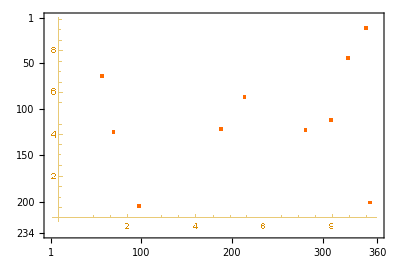

```mathematica
MatrixPlot[%344]
```

```mathematica
GetComponents[2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
segmentation=ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background,axes,labels,data},"Real32"],{0,1,2,3}}]]//Round
```

{{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},233}
 |  |  |  |

```mathematica
MorphologicalComponents[-Graphics-]
```

```mathematica
(*Evaluate this cell to copy the example input from a cloud object*)
```

```mathematica
ComponentMeasurements[-Graphics-,{"Image","Count","Centroid","StandardDeviation"},All,"Dataset"]
```

Dataset[<>]

```mathematica
MinMax[segmentation]
```

{0,3}

```mathematica
Colorize[segmentation]
```

-Graphics-

```mathematica
plot->segmentation
```

-Graphics-→{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},225}
 |  |  |  |

## Other ideas

```mathematica
plot=ImageRotate[Rasterize[ListPlot[Table[x^2,{x,0,10}]]],0,Background->White]
```

-Graphics-

```mathematica
ImageLines[ColorNegate[plot]]
```

```mathematica
{Line[{{0.,16.76000095879914},{360.,16.760000958799168}}],Line[{{21.979393760619676,226.},{21.22886252403712,0.}}]}
```

{Line[{{0.,16.76},{360.,16.76}}],Line[{{21.9794,226.},{21.2289,0.}}]}

```mathematica
HighlightImage[plot,%]
```

-Graphics-

```mathematica
DominantColors[plot,Automatic,{"Color","CoverageImage"},ColorCoverage->0]
```

{{RGBColor[1., 0.9999994542917262, 0.9999990613752895],-Graphics-},{RGBColor[0.3999997979338314, 0.3999994754160956, 0.39999930595934846],-Graphics-},{RGBColor[0.7019605099695899, 0.7647054401821617, 0.8627441855551392],-Graphics-},{RGBColor[0.3686265049386595, 0.505882043771485, 0.7098030258061783],-Graphics-},{RGBColor[1., 0.8117638099131591, 0.6156855836985293],-Graphics-}}

# Generating Training set

```mathematica
NetModel["Dilated ResNet-22 Trained on Cityscapes Data"]
```

General::mxcacheerr: The cached definitions of the neural networks functionality at /Users/jofre/Library/Caches/Wolfram/PacletCachedData/201904070164/MXNetLink_12.0.0_1agsyq8ky7art appear to be corrupted and will be deleted. If any neural networks functionality doesn't behave as expected, please quit the kernel and try again.

NetGraph[<>]

```mathematica
plots[n_Integer]:=Table[Rasterize[ListPlot[RandomReal[10,{10,2}],PlotRange->{{0,10},{0,10}}]],n]
```

```mathematica
plots[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Rasterize@ListPlot[list]
```

```mathematica
rawAxes[n_]:=Table[AlphaChannel[Rasterize[ListPlot[RandomReal[10,{10,2}],PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]],n]
```

```mathematica
labels=ImageDifference[Binarize[AlphaChannel[Rasterize[ListPlot[list,PlotStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]],0],
axes
]
```

-Graphics-

```mathematica
data=AlphaChannel[Rasterize[ListPlot[list,AxesStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]]
```

-Graphics-

```mathematica
axes=ImageSubtract[rawAxes,data]
```

-Graphics-

```mathematica
background=ColorNegate[ImageAdd[axes,labels,data]]
```

-Graphics-

```mathematica
MapThread[ImageMultiply,{Image[{background,axes,labels,data},"Real32"],{0,1,2,3}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
segmentation=ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background,axes,labels,data},"Real32"],{0,1,2,3}}]]//Round
```

```mathematica
MinMax[segmentation]
```

{0,4}

```mathematica
trainingset={1->1.9,2->4.1,3->6.0,4->8.1}
```

```mathematica
testset={3->6.0,4->8.1}
```

```mathematica
trained=NetTrain[LinearLayer[],trainingset,]
```